```mathematica
(*Intialize Parameters*)
omega0=1300000000;
gamma=0.04;
num=1000;
(*Generate Microphonics*)
delOmega=3;
delOmegaList=RandomVariate[NormalDistribution[0,delOmega],num];
(*delOmegaList={1.8337842711923844,0.16040558965706472,-4.307908341842026,0.11196228241045321,1.561138822537817,1.4310669691969455,-5.7148967438072775,0.8582591562631161,-3.1588455829376096,-2.193220459639862,-2.3874198159479487,-0.4594103566831291,-0.8567670604780513,1.8962976312195614,-0.9675978637283402,6.4967385221613805,2.6308426784814403,-5.315457541803884,0.14877809981253406,3.4586540755423596,-1.9763995652867556,-1.7703260895866786,-1.2697226585117203,-1.4319249287682079,0.4872786615967301,2.248867017802032,4.209274592225637,2.509369157743081,-6.43760565854395,3.00752514460268,-0.4288443603327109,2.571955129627003,-8.354181836965537,-0.8151147188061691,4.917101291376647,-2.247840706526191,0.3445708796402092,0.06636261000942495,2.9259216429179284,2.4481381548071486,-0.5307403294688801,9.53266693167888,-1.4848679160384757,-5.148696811269671,2.664465544942553,-1.3892761152795494,-0.7208615972501062,-3.049651152725635,6.735963439241332,-4.827639863875446,-2.6323693251798064,-1.4284771084745165,-0.15350354214058645,-2.606694892591875,-3.459926913089396,-3.05414153179061,5.04789844954254,0.9531538374792593,2.7537997766399243,0.5107818935900516,-0.44735505640171225,-1.6215342158654373,2.0714784950665304,-1.9460271486894982,-3.963666115099412,-1.7890037853915106,-4.791345740418593,0.5223967107571051,1.6675504168034656,-2.121277320845488,1.38126156401793,4.832778208957681,-0.20548456908301777,2.7593436754886254,6.665687056328942,-1.4746369461214488,3.6549294687506775,-1.8821815883658475,1.1969011544116037,2.6476177207444613,-0.7214190110218488,-4.233245283550327,2.588713816890586,-4.601555082081442,-1.3342466475440133,0.35146267034144857,-0.568685653178279,-4.015235766312606,6.342733304058968,-1.6951022748844053,-2.3369422830567705,2.0884683559287676,-1.5102724529171085,-0.8670394199327418,-3.5072961929010087,-2.4481776515077764,-2.885830082859981,-0.9674307132587606,-2.4083446123618057,2.1889659221206546,-0.3935106615471991,-4.347160742351832,-5.022117173298257,-0.5903653586707219,1.343348771993563,2.3995252125469144,-7.251578832675323,1.886214242970286,-0.29765504597104325,-2.502454949420456,-0.6156715747535441,0.15160470278582214,-2.1926391373487712,-1.2063880082916587,-0.38431461514770887,2.8256911698602765,1.3538318783152248,1.205200058068403,-2.4764653431714985,-2.4797639308321764,0.48150313502457065,-4.847395039528184,-1.3159485058633524,2.2203192902222533,-2.554199053979861,1.6276281325248496,-0.8094459383765011,4.4790207470256895,3.8759186972084825,-3.0719425771470217,-1.1384969075399767,5.8621427509330974,-1.8422995147304437,-2.7040330598963886,-0.7276934762173936,4.5018662332797055,6.743665099639044,1.618349939595698,-3.728289549963677,0.335703157424312,4.283419466523518,-1.9157378837071237,-5.909538683142119,-7.844599645803942,-0.9935444892361326,0.8550952299260778,-3.248482883798386,-4.568206282037243,-3.784050444233939,-0.8500747702709601,-0.4518091970332411,-0.6494564083858315,-1.3024606601327557,1.4696432900945324,1.2269712773250936,-1.6484747729683975,-1.9585091125916667,0.1305853121870482,-0.6369776096753879,-0.8715083559254436,2.320291482197998,-0.8209564099027857,-5.714203404781412,-0.240681789180021,0.25150144864431345,-3.483134253860338,-0.5773664390837367,-0.023303407870624945,0.6528556814429264,-2.2537688328516574,-1.6836134987790579,0.469905619816926,0.3392803379303015,-5.191572306972103,-2.983064999064357,-0.9458056105959328,2.6928820269021387,2.1706202066051388,0.3273096866415608,3.941481435263504,1.4668971919614229,1.8415182277184525,2.671770817150764,3.577649972718114,-5.29641404488007,0.31713265489818937,0.2766207326094653,-4.405279356845044,-5.94695365847964,1.5632966897491043,3.8360192561476745,0.0693302732064804,1.529196414088325,3.245235919148267,-0.5840817418418215,-1.660034961798373,3.5009760602784006,-2.7554926126756683,2.750996089351796,2.379953405553299,0.987300854074396,1.4073370140930441,-2.0753649701970445,-3.8870555550386356,-3.8316173747151385,5.076493640525638,-1.6160286710457346,-0.08011959035945583,-2.510218577287877,-0.0229124504355943,-2.4291564202141895,2.362297032237792,0.8720819286400965,-1.3734637122129243,-1.1038276946331842,-0.6834390310289616,-1.1348046276961046,-1.9787936960216839,-3.0225221053351006,-0.10137647193398795,-4.099997505031015,2.783686864262384,2.0882093675031617,0.7589809897466199,2.930984919991195,2.339326035269902,-1.6228519501087908,-3.293794591108371,3.1402170958332816,0.837725269300635,-4.316523327049457,0.5185716749043685,-1.7055958238280666,-1.500259602922483,-5.567834890811386,-1.1061265683501607,4.039639426139697,-0.6499980766164946,-2.0204179180997315,-0.25060961119309627,-4.882108589274432,-1.014354587171493,4.328041319720766,5.474903795074114,-0.9021656862190787,3.3399894568083384,1.311489723479545,3.0623673791231907,1.013027090496859,0.32408578903985485,1.620408639445604,-5.861771761975355,2.076255676625802,-3.3120709028849253,-1.3558626605279678,2.60734872700721,-1.2624544626464966,-0.7228975999281222,-3.8759186098982856,-5.733910004559364,1.5489654161404294,-0.7989867035376578,7.111874458321575,1.29694967376884,-1.4171058859772914,-1.6228317196757327,3.8982581245452774,-2.044855960531852,1.325907109143953,-7.902707415732034,3.783697414932371,-4.032615037696249,0.05436734889506481,0.2517705441190935,5.018968847364759,-0.28727401038846134,-2.4307284484377645,5.884776059130222,4.99880676359985,1.1259181222997177,-2.634822114805469,1.3151607755733175,-2.430473107115997,4.4787811734999305,-0.24198942007572147,0.3822786511874926,-5.000522073937068,0.9912854494104625,0.12052230418648893,2.730545324333998,-0.5369980137677605,1.5181286090991037,-1.6222703450019424,-0.09786914463707777,-0.9682302101544535,-0.8338676778553885,-6.008833378535652,3.839345373772248,3.911000375605835,1.7537613860887455,-0.9666008985800307,3.1831946538099203,2.4988912872256384,5.000815797819219,-0.7826038413479375,-3.5750180430544147,2.1025606946906525,0.11688200977809092,-3.690926402265789,-2.1783894903036205,-0.4817099389610667,5.182322689874413,3.012796223914801,3.479372271650188,-3.63458776893185,1.4526750281611431,-5.830629273248365,-0.46671811244253064,-1.4042708671905533,2.3160530102651156,1.8392893719041998,0.5623237713435795,2.2878293826635105,5.697513435077266,1.8889631541991911,-2.1251893450209125,0.8471611193444996,-7.747479262701138,-5.812533814466779,-3.42539847831729,0.9389106144141167,0.12738337720343865,4.058981987814869,0.5277748431404231,2.387873858847695,-1.3911248291897367,-5.885064998919442,-5.131338405955813,-0.9749440479298326,-1.4905571064738152,-6.227606475660418,2.6571615274379163,-1.5115767337987671,0.37340955857850117,-0.5750650075812758,2.2886737749802464,-4.145804102994337,0.5630446035594738,3.69289367920174,3.692933006074424,-0.2307140892760464,5.290458654166197,4.18003453528186,-0.7341302889279254,-1.0584764839525587,-1.132004137722375,0.6654546474596293,3.071747755495761,-6.119104999030945,4.748649690032834,-0.8950242481792364,6.17824457818765,1.05431886420234,0.1379382408086227,5.493944366143621,0.6875612356090467,0.39826213780562,-2.3140061946990156,-1.5619643442359723,-0.34541501680071346,4.954492704866755,3.8972832014022285,3.629445090381269,8.75315478688308,-1.37089134994954,4.076803433733393,-4.829859420893151,-1.9698774052156653,4.273551877604563,-2.2014456314203708,-4.319373497695906,-4.025896371665825,1.4979196001518105,-3.6421974927260616,-1.361643297085396,-4.526073389292419,1.3872144504262567,-3.5673228839246462,2.8071372752080253,-3.214650262478729,0.14374523720408983,-0.39557004572991417,6.608468886179549,-0.5841893064044512,-2.325065590432254,1.5166795377778202,3.521645655845219,2.9930989711759706,-1.8108621406428742,-1.776468723780866,4.563119376685883,-0.760797632322891,-4.04453603531097,-5.710668441810212,1.846590573564812,-3.735512451932257,-2.6724530778822997,1.2095882491789454,1.6074233170995864,-2.384520114753251,0.6827129360325044,-1.524227062121807,4.232550637735286,-5.191378268481155,3.9766858658671085,-0.15952437212390758,-6.765625330237434,-1.7827378255775967,0.9317884421933651,-4.734879298610872,-3.7167114661677214,-0.9102782178854797,0.23620585094655247,1.3873246736337013,0.8441247478853624,0.7907372000882996,4.829468305415686,4.447857358689031,0.6197305679018791,-0.5182908984605287,2.158655394909051,1.9302692067628127,2.06561985048945,2.8554090421957143,1.0712997213851745,-3.9917935249311385,1.6940233635804305,-4.4456543982317855,-4.884604915624257,-0.10665911398826622,-3.5386434995126996,3.8041114107636003,4.514089110326565,0.715817704409119,-0.09109085333261437,-2.8956134557656457,1.5674710336769562,1.7166693220824296,2.8931858198891636,6.693374078833237,-1.067974475076121,2.375417510616608,-0.9749985723497195,-3.936569375228149,3.952650298422117,-1.7445789372822276,-2.270521259285947,-0.6905308536333256,5.1402469808129645,-1.522506764444625,-1.326531214761503,-0.7110881419992032,-3.930926643972971,-6.788283804105907,-0.33846081470445516,7.399733115435776,0.5457716706853425,0.204940142485474,-1.5296479429822696,1.014613327732743,2.2376976410126304,-4.273144674746698,-0.4716915790445606,3.3276760549444586,1.0738492632926662,-2.429314699609758,1.6864871686073564,7.5097350693586895,-4.538147953239884,-1.124802194551634,2.5087859738925595,3.1309832822807,-3.44157919807983,0.04269342735279393,-0.7030061313989188,0.8662162794921878,-1.983528332630112,-5.377466918710724,3.086003979481636,-0.6576649722246768,1.9870480742264442,3.2783846125251523,1.419514883766854,-3.86904876704799,1.065557765543805,2.603525466973217,4.83939419756785,2.3748655606397584,4.068621080356825,-3.2275704140487704,-7.074823596303612,5.90814702145547,-2.300603540862048,-4.232112412436074,-2.4453819633011333,1.9660402306377613,-0.15897426444115878,1.5254639038955193,0.15245321989178576,1.6234302282416584,-3.0124420456126537,6.051608221652054,4.105172844594888,-0.8066181186003284,-3.5887090890270903,-2.598582684903626,-4.40244456648331,-3.680015083975707,-1.7377706869404517,0.03913478546759972,-5.153107601225522,1.218185729261683,1.8292108762608734,-3.8000643210400136,4.57618069974544,-3.3631957742787773,-4.621321359130867,0.8102252894681847,-0.14778997528124718,0.7413724199714353,0.08254569145915697,-0.8066484909728296,-2.8861639087635274,-1.3224868123891993,-0.21641831370803596,2.921404302732341,-3.976500301487154,-4.353017129780817,-0.4461450215174098,0.2142207363526322,-1.4513139855649457,-2.7408773932240496,2.3544446942439876,2.3767803324776824,4.710218594418128,2.3016379359636314,2.576792700847864,0.007109400523798782,-0.11509805808400075,-1.300796314282306,-0.3149940256941553,-4.643965650482208,0.9951551393705277,1.9871304470756206,5.193278226430385,0.25256087249337933,0.46580332813544467,3.3376617052149244,1.7225735117057432,-0.8386377349413473,-3.0052048937474862,1.042560516035824,-2.8646622410562625,-1.6131253247267672,-2.17257762520914,-0.7422615729241785,4.189221775917799,-2.1981982068023806,-0.9769254495140327,0.7464638706074919,-3.5385154621907096,1.4488949153274866,-0.6823869903071227,-0.92112233433009,0.6831073219010448,2.5314731210879873,0.6541832761656412,1.0250744667222755,2.4542130165444433,-0.7723091830241057,-1.602148303623446,10.789404044035576,-0.6517753149539379,-0.4049690648389,4.393483220456173,-3.7430590839825366,5.1415130689486475,-5.5959249495059975,1.1775104180181934,-0.7410875528176712,-0.8815387920312577,-1.349654632711521,-4.73104699924736,1.2634411146192688,-2.5552070497460937,0.40763768965114033,2.1164219438173406,-0.688891022370738,-1.1697863120331116,4.6193648808554535,-3.141375932697392,-1.6362565227411643,0.7899589098328309,-0.30563924134646236,2.493877032987097,0.8735452955357108,1.715481329605591,0.8120984939179262,0.7810497273512135,-1.71588804442538,-1.4348637097218147,-3.1046757842903943,1.9423915645069325,0.5042574785310182,-1.91898576673103,1.4490458527991217,-5.225963252791075,-2.0469632677886027,0.297633576469192,3.0855214678577827,4.60148042544218,-2.0789494292224715,0.06993928627399719,5.249224005296972,-0.9862319037183345,-5.444585166163087,1.387516172286948,-2.9559647482297193,0.349296349747908,-1.5233362244439064,1.9681887162423357,4.009279555659557,-6.247403291572083,-1.8703700465607946,-5.933468121724765,2.7636993025887238,-1.4766675996300815,-1.4811688207414146,-2.3868609805160403,-2.5849356222893154,-1.655291130173672,3.4268180173822267,1.5751766203951783,-2.585242281145018,-4.961999509694162,1.4129923935929463,2.6475319341383226,-2.862394280937675,3.83126585356322,2.5223316108100473,-2.4985700007001133,0.6358510122076252,-2.645738181020123,0.8514055701514939,2.178683656829903,-1.4588408172923,-4.1038037874679745,1.1719127793811963,-2.4308656448103303,1.5223171272948728,-3.8464942299035885,-2.452589294659838,1.3933581051454753,-3.941961489807476,-0.7563045807066022,-0.09115221408331727,-4.148714910677104,3.7000338252628184,2.112118766800305,3.8091212028409585,-0.4398568234255165,-4.76446811718031,-1.3991599520291145,0.24171093597131976,-0.33747234142858656,2.325246961643699,-0.15159795011163715,2.9274211815920665,-1.1256224109207846,2.394136102572598,0.6318189535595236,-4.4421817133086865,0.3152489285834816,-2.8249183857444606,2.9004559432170036,1.329241121165397,-5.915704768561628,1.0410158937914504,5.511158544640868,0.4773085278485801,-0.08549181235863229,-1.4616982157718992,1.3941135348440494,-0.5635930194760452,-2.64543364461347,-6.630932585362731,-1.822377053125179,-3.0214255867942206,2.7044735283473327,0.5952987864980752,-2.875568339256224,-0.79689820085912,2.7517856657258735,0.2627624488724053,1.7718722328555143,2.704523239971324,5.503608128643478,-4.490521993564673,3.7455317866912106,-2.3510607687937406,0.6436209428130216,-0.36170248950066947,-1.9131202204554578,-5.846203194624535,-0.7652857486956791,-1.9299894719870658,2.0547262555590975,3.407048333566901,-3.1290218017036913,1.2397070213146568,1.7687497436887083,0.39780629517346505,3.0081105887261606,-2.313236176051814,0.7590623542603631,1.6873898609980384,0.1935854409625918,-2.2254315109625007,2.087598237343026,0.6988085267556892,-2.2880900662075114,-6.398085896853747,-0.867220906493746,0.9406752180904208,4.182386372076701,-1.1212659053871996,1.8682385356827182,2.615997208886906,-8.40131753789812,2.722487543819812,-2.00254807032611,0.9860159429410634,1.5568747053660656,5.390603187837607,1.9754053715324076,-0.4912095370038308,-1.0992779775225063,-3.6204138934725743,-1.026560916725386,-1.3191665402096195,0.043505250763187994,-4.752682801607533,-0.5060168266697784,-0.8730436476115543,-1.1176361779440698,1.7016903825569685,-2.060394920378545,-5.788304243151975,1.5189501837117947,-2.6166952376321526,-1.4249546176546866,-2.814465838621563,1.6594566633166947,-2.663107031200839,-5.1397459214033265,-0.7313405265888046,-1.5318074112318023,-0.6208961699573713,1.4672544463844304,3.008287047865701,0.38049816613332565,1.7225566968264363,0.1465820774069805,-0.022503378478161022,4.737078529242832,0.04142145043257308,0.17425673039065664,0.0769210209854827,1.8618113509249425,0.7574570909012516,-1.4538405092415472,-0.7742194529804342,2.6165387598746968,0.17142934880744887,1.5125211112551702,-0.2076653790882838,-1.8433455674637067,1.9866822529350079,0.1221478257410209,0.5783909077638666,0.13446316900091168,-0.2214442633533019,-1.0904629250553595,-0.23748832270552767,-0.2800906998861866,-2.757469343094235,-6.187504027836837,0.16712418273603008,0.4321134929235092,5.886948547992396,1.9067669913079326,0.8896959674524918,-1.2316718539992395,2.3224711784883896,-1.8461327198545874,-0.10113892662043417,-3.0659191967426866,-2.3196048636845013,0.674299122927068,4.393868302600506,0.8767148216561764,-3.158294374586651,1.5797945529134534,4.018236000882259,-4.956673349875822,3.8400718050591833,-4.780591689626682,-0.245145097687313,-0.1826809147685115,-2.6020123283351504,-2.532168975252678,5.103207373380753,-0.45856038972043667,1.5377728165091862,0.7283341723128144,0.15284808814024423,-0.8296744096504964,1.0940899611878294,-5.142743957489677,-1.4575763981275789,0.4824208515861691,7.090709084448258,0.7366609592690101,0.6152616784641943,2.653884949600923,5.803130316063115,2.1187044425241015,-0.5965264073239609,2.110303321669615,-1.7154204964353992,1.0893311289808802,-0.02451044241460966,1.9403758385711936,1.4091990597078963,0.407089410176289,-2.4654863880830313,2.8506574255832198,0.0419133212259752,0.2887125344389019,5.311956110374284,-4.029664525728389,-0.32915837524574804,-1.387995770681301,0.6078654532875692,-0.7190037852802185,-1.6692170959524402,-5.656468062314601,2.3272954423963212,0.7580866145582302,2.4920919132455257,-2.4824884509976273,-4.054401278279239,3.3666071603083445,0.20709846093297582,-5.1669687027749545,-0.5902259662201077,1.719047046455118,-4.1079906645052775,-2.2555029303300222,-2.3235045324651775,-0.2274561318580631,1.9306818594261421,-5.144876121203171,2.444367287501149,0.4427941210834199,0.05701484776094251,-1.4506543265392324,-3.0789908906601404,-4.933231703274233,4.692663898539272,3.270747138041558,2.7691406505087124,0.049377181505704866,1.980497083424002,-3.3472444520852704,3.8691270089880905,4.048317285494224,1.2283274510539821,-5.71850877635026,-0.764838590452014,3.625484541972443,0.038901230722744644,-4.310408040940087,-0.018876181765666973,-3.005259227187286,-0.4326752749217242,-4.137440085850108,0.9235163813264804,2.4229014698175764,-3.4162838744419557,1.582289938333291,1.557476369919039,0.8171785458833569,1.80901039947144,5.112385616155454,2.6921292912265757,-0.9001897113701987,-1.301456800439701,-4.997894926434394,-0.6026743601801908,3.4805609319171746,2.426217950174236,2.889423125386176,2.6821057933252037,-3.6141185697189693,0.24230618333822496,-4.989077344322673,2.5518095857130962,-3.7184930016105455,1.1832537563263206,-6.066314588185512,-2.000057087854885,0.3187832322774389,-0.7855587729465757,4.721385648722181,0.44611180504856907,-0.42217990673282313,-5.819227866638014,-0.327464044398571,-3.7198535276783447,-0.7744556347179852,3.0564920936132327,0.828891833174702,-3.4446850701442084,-0.8335106200633917,-1.0177215027817723,2.146835014400904,-3.49039687256187,-0.8104274173801994,3.383171204408222,3.2984667278250743,-0.5379002935065101,-0.2695060717734491,-1.2447556179201096,-0.9423649300576138,-4.034559816721609,-2.472588597483802,-4.0576614782386295,0.6775113428086939,-0.07211185515880307,-3.2958031574503956,-2.705474109999967,-3.2355859846828756,1.1875235154573869,4.4799841739313875,-5.691637716109592,1.5759805393931274,2.9108255954031064,-3.27478820116257,-2.5688289721592867,-0.10331496711146516,-0.0968247012067883,3.6151234601562723,2.4032261248238083,-4.26871029537981,-1.4658239839907992,2.572876310579146,2.763718001434019,0.6445613256586562,-3.1587490088554295,-1.5037794447118966,-1.4370312387277728,-0.9164508520937535,2.1724493193598544,-0.13430171503323157,-5.472388351003915,2.0670605438555363,-1.4803373664316772,-3.6413638514788955,-1.2397064244116964,-1.6187275768317728,0.2749545113493899,-5.4939941574701034,1.4871673334673374,1.0796690058152694,-2.980566857170749,-3.4021477088987386,1.9072862106059987,-4.853857972160692,-3.5572851896565316,-4.684480361550875,2.4588714815145076,0.16485028737573199,-7.823770652311768,-1.5891900028402937,-4.792186724158275,-0.1060834634867179,-0.7720371431355038,-4.390884390707863,1.8546322479559372,0.6943112707070361,3.0430547033027526,0.11380859606601396,-5.625573717018,-1.1000097338343815,1.9806910936196866,0.9639456050089436,0.7643556395716884,-1.1215465199026058,-0.9689813024174787,-3.777341282661086,-0.2517493883513765,3.0918889363554505,-1.3428300923340648,-9.321515595360433,0.24834022332298447,0.16282039093343753,-2.508652466966731,-1.1026758676430581,1.0033558034663794,1.624615189516731,0.5739648357184536,-1.1998380978129577,-0.37888058681208203,-2.1909245276914966,3.415021691183071,-0.8188896308717284,0.4544176480619983,-2.086494338920336,-0.4355820738082475,2.566280713561815,1.8809763490944076,-1.4848079585181906,1.8840794429652683,5.859911221267823,5.277673984697487,7.328773847304508,-3.7686289031058107,0.434783493488866,6.106498352168259,-0.387807603465199,-0.5606800523085095,-3.0906656551393055,-0.5858132044003568,1.0370553766445132,0.8091010691399709,4.134508071456041,5.411282366395174,4.870421235845309,-0.1905046904565309,2.985192496542319,-1.2908850445951492,0.9138667692036814,-3.3272985058039066,0.9972769539035363,-1.4298392089068257,-3.432613625410997,3.9592092460705612,-7.45691795699202,-0.5773314173003409,-1.1954630034373928,-1.7965204078193735,-8.018026645993505,2.2335060435795557,-2.604251442421664,-1.6618910926464527,0.21103755063494178,1.4466215931830695,-0.5261522117107319,8.592787428015296,0.7372270899336032,3.6003000274798698,-0.8980289361965766,-2.467658801704607,-0.05361505013987474,2.3187372645145152,-4.776935293065151,-4.773610856075842,1.0332775767201174,4.947905734603235,2.8780042861778226,-1.8789239198296408,2.691493157549322,2.0195134058547675,-2.377186318035971,-0.45951345302319985,-1.6027959565077023,-2.224095756143886,5.106734855517866,-1.9768820416267274,-1.0984645615512363,-0.4811520829418971,1.5069075147559805,-1.1799526158639344,-0.022308866454111426,-6.439613594497311,-2.049615994641915,5.269927982033887,2.8975881057910673,-1.2953755397244364,0.749571305376206,2.485633269487332,0.7956311337612769,-0.5600811956437008,0.4886664165610681,4.677853283059826,-4.200829151580166,-3.3517485880553624,-2.118384452270515,-1.30139119515098,-1.3325464193177823,0.9106860178824582,1.4244661315219591,-1.4433523214257769,3.4606319708871136,1.8518510269888933,8.469761192551086,1.3453849401490345,-2.352593817643269,0.5507575799496542,-0.3047702092947719,-3.4704619927390024,2.0785440487868327,0.4578291690431986,0.5284229864567538,1.4329673260738156,-0.4537520999273287,2.3707078121438268,3.184562718613114,-1.6038730215597703,-1.6704628904696683,0.15878545458844573,2.69530309443596,-1.140212267620366,-1.486936027448959,2.0741614718874932,0.4055659143690679,5.844529822964629,-1.6701841319369222,6.015831758137432,0.13917782679456464,-3.14259540997633,-3.8817236271179953,-1.352190241880127,-2.03672821340477,-2.9529774477803064,-0.30939981114534454,-3.2952501888542067,-0.44585572611586716,0.6027952426783922,2.238088919744758,-0.24101279959291605,-4.585368247118467,1.802554184087552,-2.636697889886964,-3.392358075727162,-2.047137476957824,1.4948901715462304,3.4494256263599037,-0.5007351923984962,1.5422131200003766,-5.081088997410887,1.2034354397461438,6.2134241186490105,-2.3583663578808816,0.6991257331719339,2.851709354425378,3.3080816277148957,1.1123468827937695,4.512932052005735,0.11948241142084944,-0.4394601690942957,0.27121338879022044,-2.9337390222682433,-5.793415596887723,-4.4447355642310304,2.620285679672297,2.462067451109526,-3.7291334553551336,1.5080977405278742,4.798515231814058,-3.084723304398377,0.7946135731981862,0.38249689802550196,-0.4881885733014615,-6.864770216427622,0.4664453621427134,1.050402819798734,-0.16019051852476604,-3.1532506262948954,-0.09140302179913926,7.491788858797593,-3.6343725292706215,-0.2446112599980343,0.8863990735229408,-0.7483391271870312,-2.692658323645843,-2.229913962597971,3.2239188364866522,-2.9060982243353726,-0.1831390678641235,4.34644981356908,-0.5778135441507625,-3.018191218776133,-1.494508597365819,-3.1839877822186553,7.4290458620973805,1.4359795320199003,3.0052080857331487,1.7916185069063388,1.5033316658680365,7.497865850190478,-0.9924312695335679,0.26736005631503007,-5.628691991101647,1.6781843417505617,1.2374989112550379,-0.06048340568445495,3.1239286897360192,0.21539096032987623,7.089435850380995,3.219830003708762,2.0519546485458933,0.6237505842375225,-5.684923304496494,-4.147287821473089,5.174939565433126,3.1152066360739616,0.4726846996583941,1.1497528190043476,0.5916972822417349,-1.6422508705558592,4.014345944370702,0.7605483756943091,-0.5909916070539009,-3.9860005315112224,-4.538905368982022,1.1808113012251504,0.5610810053754676,4.832043221947228,0.05388406707317589,4.913624142463302,3.8027593729272557,-5.421275701914176,1.3509492508108154,5.368410000926194,-2.736675845194407,-1.2550205453902163,4.172048785420633,1.6015833928143632,3.400811020706369,-0.7530645796259894,-0.5496518749392985,4.137053675562548,3.6483605212507904,0.42283049469414496,-6.7865052757247115,4.930877096272568,4.2964751619512445,-6.561820692547048,-1.2881750938693053,3.21028195702963,-0.9731117910239545,1.965561092693521,1.6333366506814673,-2.776683636143842,-3.702946311016413,-1.7532722497788973,-0.01970035889274989,2.484298680193968,1.0555495350764281,1.7313581282008086,-1.0609767010501112,1.2671114627530018,1.0649797003882295,-0.2396213925983542,-1.1808090827693085,3.60801522670005,-2.4821828704571494,-0.8757772362108351,2.0666468819570234,-0.03869174988633934,-2.1365263214849985,6.884698335195673,1.5877726274659472,-1.3226256219301267,0.005969330138127151,1.1781213953587533,-0.9466341166049609,1.9536286963992529,-3.0654690570368603,-0.09009828580744025,-0.5153109444562255,-0.51551420669276,0.9028424631895949,-2.2254078160044455,4.031247235410102,-2.120818224079054,4.041457506252333,0.4538800865776668,-1.9483562778457224,0.7108060207442138,-2.159268651894649,-4.108925032937473,2.4605164388266223,-0.9702245958478249,-1.3186380268337128,2.5433914308487804,0.42399797607319445,3.0574212355531056,2.5667342788390055,3.555030942614313,3.2335962914079603,5.5334090492835895,-0.2832409365369626,-0.9037652864959598,1.4632201594612528,-0.017640427713665915,2.5888221238634257,1.050362875892401,2.9324299090103323,-1.0137844624935646,-1.677190448262637,2.573268867720019,-4.598853057867086,-2.8006106865482545,1.3803079915396903,-2.022032563485458,-0.15481097518370251,-2.486112277610164,-1.9036033301164426,-6.493025231674558,-1.0444325796279057,-4.588300173770313,0.8467319118074239,3.0739435064072045,0.6963008384676087,0.6496696805842437,0.9827341887956398,0.2266942891819137,-1.407145223636264,2.7754892405906593,1.0353907218038256,1.0545091948951584,0.33307469248882243,2.9003733738726996,0.6035021262141348,-4.09536207513173,-2.302625918452677,-0.6316128370086568,-0.6456183765563994,1.8694386735876298,5.348959534502117,2.807574242490509,-1.305399078105199,0.5262115352387408,9.489901442019889,1.402548701970422,-0.03833763333910035,-1.138961877143531,1.837107448543817,-2.7087092446004806,4.063045783545677,-5.642887247870637,2.03847317691471,-1.252077420011533,1.3899039922201963,2.26756735798445,1.4242505082038237,-3.3463135268031974,2.4255101298862636,2.882810701848721,5.264826785639608,-4.306102916854517,-0.39111560502041914,1.028264111027817,-2.569562618683046,4.283807221340802,2.9819218115149946,1.4105435736942429,-4.374196483698056,-5.512272134282135,0.4473611229119988,2.824178509595584,0.9450651275593304,-4.953540386544049,3.0300486065425405,-3.122863637864741,-7.026192949666253,-5.225568846730456,-3.678254776660266,-3.7836922590517603,-4.8650300443306795,3.1730838192301887,-1.5202315184881297,-1.9916789424988444,3.047551161109307,-0.43381502728822224,-0.03469850406696958,0.8425136658027598,-2.7816366699716593,-1.2806393230487307,-1.3736122121462309,1.8921580350958807,-3.011867325066211,-0.6357015189118184,-0.8023694094785572,-5.716557260645691,4.190651305725912,3.073265515436144,4.7515363987168096,0.7817871926671794,-0.09265388060863333,3.967533427133964,-0.312834294201262,0.5296548103990286,4.47213420885739,3.160558608542524,-1.7433868394818712,0.879483437669076,-0.46890038651014565,-1.1075141297504811,0.36726298586208944,-0.8499939793083118,1.8395552527026218,3.3751166428081256,3.668589726306121,0.9328320924468712,3.339582265487435,3.1502150047778015,0.7388995277514248,1.7613889056889276,1.1819115752626803,1.3395238362874056,-2.3814939526265384,0.07573136894789616,-0.32195711767409657,-3.4321240943660585,0.688375653410967,7.157113260817838,-1.9307996602913047,1.1169015077727076,0.7923533937475712,-0.34236217085153786,3.1361880412148864,-0.9419947340786708,-2.5612226589898563,-3.557023711460703,1.819015807243845,-0.1769436879595233,0.21042539749406278,-0.5422720709141766,-2.1237481457542366,-1.002540163516293,-0.22380602538735012,-1.0414953855373457,-0.6243125226762393,-0.9172401381411684,1.1078804198772885,-1.8704641143327412,1.5639330984775712,0.17636497450524566,0.45254652331233086,-0.9518794277207825,2.9207060130612446,-0.6318165623005126,1.5771948151750477,-4.190644507639879,-0.2760669406031919,0.29353088983625436,2.1471302177213065,-0.6038980609689616,2.5473672075829157,-6.332358622631013,0.39403354777002736,-0.38317861053384566,-0.7156095344030016,-0.20403285654466077,-0.6197931741804672,-1.4473551673907272,-3.79655660187235,1.7176904082008901,1.1579884946410133,1.2249661593358157,3.9583341632365863,1.0530547381987216,2.400926530953134,-4.422113074785726,-3.381454299621463,2.3057480769582246,4.731617743538188,-0.7569177622894351,2.690307061546858,0.42645596305467054,-2.420136704501003,3.1155568333768167,-2.8411297326208795,7.8074836439430335,1.7004825732115554,3.4671867186159124,-3.5139663958134735,-6.176208117597358,-0.6492953379691818,-0.9966465883455995,6.501172753334525,2.482047568927859,0.664970611258059,3.7880922472094736,-1.0455146931855501,6.332496398882582,2.0516316193614803,1.8812840026260342,-2.0160039178306866,-0.5319446385288429,2.288463692800528,1.4126986528507008,-2.544726633464424,-2.0393687396578213,0.45286824938663905,-0.8398171920824399,0.32163846478750047,0.09891510446302143,2.476823935144911,-2.3861626220288974,0.05865968512096012,-2.2657227944319476,0.03881169458596145,-1.9687270167647979,0.26552092128216465,-1.3310179896666776,-3.359345976211176,-4.0303605836653835,0.8140068465154678,0.5321559374257777,0.7680609155567845,1.1707444786694292,-1.9642620578292056,-2.970331163097273,-2.7769576609698023,-1.5255771529608508,0.14639760337093385,-3.4035756401485426,0.7924920301670914,6.777587256522021,-2.9441037264898533,-4.167095115251336,3.420168663172449,-0.8857749504597292,-6.0001828163471185,-2.3153556046611903,1.1074696726450504,-2.278125941475197,-1.983946196317051,0.4260370844514901,-0.8228137281477274,-4.404219587359871,0.8295854136613616,3.1533913636158384,-0.480527847414878,0.6411289207297093,-0.5277602164245607,1.2517836933295599,-2.1715089071979214,-0.9396801232466043,1.478175444014582,4.5774001604381,1.1657615094442049,-1.254586237275998,3.4155527370704957,-2.4108434335413382,-2.112463026436144,-4.666505165253264,1.720179108227828,-9.109054684450616,-3.0181447560845145,4.8575126461685985,-1.7126831772790185,-1.689504876157779,-3.0846266071395423,-1.8066839393801342,5.312476016691534,-8.344346228749822,1.6209189478976045,0.2940351903509739,-0.46072698567857184,1.1001726988261722,1.4337678841817945,2.126830096507134,-4.942853086036798,2.290433283705456,-0.08323917857634489,4.471803260499057,0.8792196550568021,-3.1427115433311137,0.8529776375532306,-0.5309842581230957,1.823841346985311,2.483727816522979,-0.6519155715748419,0.28312198631127633,-3.121237976965579,-1.0299481100076313,-0.996912136355184,-1.2046255440949913,-3.5414677501256517,-5.973684508711081,2.3944437899144453,2.9331925794695763,-3.036602052497065,-5.593452808166108,-0.31560794720577,-6.364005673601344,0.5672967576086572,1.7524500664247868,-3.319272328374451,0.314643969084338,2.7063898755322393,2.4969917046104264,3.3173969793884512,-3.8865646120734327,-0.38438796548884746,-1.3420842397591102,6.210278876669114,-4.601990558833233,-2.3983745155938596,0.8740895374853164,5.4021076686542155,-0.1321876160129913,7.345594275878349,-2.8341631008763026,-2.7202979522561037,1.6264462375071735,3.8257716841210603,-1.6673667868210098,0.4574214543663206,2.5654930269807874,0.5087617836498228,-2.419307669657944,-1.4201446680230896,-2.993293372592093,0.911496005714294,-5.262646705539134,-0.24553942884555016,6.896884771446394,2.8562312422107867,-2.161367645990808,3.788121387476351,4.516489853539274,-0.9836091659044465,2.7365922779399847,1.9611638945240966,3.237055017120553,3.9487680754780596,-1.6961766611448914,0.7042936990356756,3.087341299268537,-4.719438076520617,-3.9027792435588258,-8.22319018627874,2.0995113666861647,5.322096214282032,0.37278960356410373,-0.9328968826251031,3.64521903363169,-0.08154100283068075,0.13118998812450564,-1.3411854414067539,-2.5202291840043536,-2.401843163346329,2.3814229425733093,0.21489264841516473,-1.1023071100583692,-0.6148343353474596,-4.132124309109108,-0.18200624623537853,-3.4001829193805406,1.346797923999213,-7.793059415546631,0.6322769676329039,4.787452846712011,-0.010087843834325755,-0.7990877080505788,-5.760804265320119,-0.006738571781346221,5.881175896497183,-0.9920985252386293,1.9119966561784683,-5.470723584009046,-2.9043086725323906,3.5027535849481377,-5.276315020194274,4.789900067903119,-3.224069533490435,0.29983172064205443,5.966476698598395,1.563120335835999,-4.614897742357033,1.1713220372505133,0.6300335861588797,-3.0091568122068724,-1.330736763312775,-2.848623882798598,4.012923629129195,0.15838873015259797,1.3367908500713692,-0.1823725218381474,2.5888992935845487,4.375556563918291,-6.11684929631202,-1.52878429626113,5.0218152117774615,-2.4552779485047407,-2.689281999292462,1.6375397244625811,-3.1863014388677975,4.849871700556968,3.005902399305866,2.6655446178504314,1.0153503891077225,1.1850530532607615,0.6054298261045904,0.6833943669188308,0.9823033391639282,-0.5088721236179813,4.964990493609526,-2.8855280794872757,-2.118224313370051,4.314038490692037,0.7581899247541551,0.7167486723094691,3.089135915813374,1.867794616197005,-0.80573232339353,-0.7819263909809863,1.5839993806780235,0.43297290699652585,1.0882819565846351,-1.9150968032013749,-0.14900723728726448,3.156562706403186,-7.146465117008863,0.37150065949371874,-4.535500191115555,1.1481197964087155,-0.43145405851760016,0.5345807283889681,0.6301471131908378,-1.1707715744608858,-1.1006603230699903,5.795924890317252,-1.9982783477658135,-0.27178619093856915,-2.82557993115504,-2.4516821262200565,-0.1299378225199887,-0.15701419748969642,-1.7239763247050015,3.1943817448418224,5.020097373584252,1.2439271069099882,-1.120581998851712,-3.2427922949505126,3.2925356921345355,-1.8207991200734104,-3.249066253035774,-0.6127286718785707,-0.9096259335109643,-0.6530951270452373,-1.8392609562891826,0.8726755293942945,-2.5213232381676374,0.47953114256211943,1.2909475732896845,4.000008527603956,0.7743330436002193,-1.900272600046723,-0.9984062143218321,1.6200955230503955,0.547295064809618,-0.08057151818107883,1.738467985680389,-2.5194876504003614,4.259609873863759,0.27737739003207756,1.8828505371537978,-1.2488282241262438,0.5784695487827559,4.804503233117629,-0.29769770430586856,2.646358072447612,-4.374876124419852,0.7815414294432981,2.8432507145282813,1.2518803988284588,-2.806452642862393,-1.0551658505167323,-1.3007852776627236,-0.11587742790176506,4.277763174930367,3.3912669549239576,3.8970647999514703,-1.482168805438884,2.674876611187083,7.849728057046406,-3.30967854012425,-1.819498838568778,2.681831773417418,-2.920544859942882,0.7292238897742914,-4.403200613170716,-5.274828203351059,-1.9782525098769332,-2.0757391201653177,3.3984861509825324,-4.7391003813246515,-2.7237926845357485,1.465541121623168,-2.6496122667897515,-1.6372579792479578,0.030956766844956,1.504090852567148,-0.6146598990252196,-4.359421941525422,-0.9367345590950056,1.2157456713756316,-3.9845586408659743,-2.4556211110044206,-0.1478886461491036,-3.047521842588305,5.386037519151163,0.2258260151624313,0.08376983421719643,-2.242276772492051,-1.595498414218857,-3.759759264336412,-0.27559329116191317,3.033359704948638,-0.7449271867063749,-5.691634093821758,-4.35496312130851,1.4940433775961193,0.6078428705679997,-1.278941473485382,3.677338333927181,3.2187631663388725,0.054974913062917005,0.04019992762392046,2.3851307041369596,0.3667407065928697,3.8681599924435313,-1.460765025235945,-5.112737380285351,-3.429015939792027,7.9208601997734505,-5.234901973168309,0.3095853863197588,-4.686999391721073,-1.9548041299770627,2.237640457785512,3.153667322327267,0.1768073182062341,0.18854184867868784,2.1384072321012977,-1.4979621211193457,-3.8964891417542424,-1.231433464202283,-0.769532800922324,3.7422913897075207,-0.06266514755175966,-3.843602770568776,-0.29012240956131696,1.772834201695771,4.122402496382075,3.485752835755904,1.256588628851049,1.514221553452138,-5.608608927777445,0.9336237191783215,-5.214446432453043,0.11812928754632931,5.177772865339486,1.8964765001095898,5.172621191021588,-0.8401171276443096,-0.4451126518391345,4.356898885833941,-1.974008422566497,2.0515136925746615,4.752648129908455,-1.0798894787614173,1.29983508283771,2.560248775747824,-4.011786873363461,0.6335009132428336,0.9784009015002921,-3.479625895467141,-0.6313668040263608,-0.05046831427081156,-2.0054321381668028,0.41657407481381675,-0.6565063389747716,1.4366534880762203,0.6410442595566929,-5.296376458278499,1.5861396855119039,5.811649513294925,-3.914643061217644,3.0182756889186426,0.8544523382107058,3.2010928091691326,2.933192193005776,1.3113264318636522,-4.209691830964236,-0.7044381381811659,2.1260335505367602,1.2816260136658613,2.739467785054385,0.9270849865018536,-3.9534143602137326,-2.6006675718405328,-2.212226844516373,0.48830637752793454,-0.5768692218674255,1.8735213390913374,3.5646692669725817,2.0940369391627884,0.09488737707271702,-2.2529224821626173,1.8573821046608099,1.8662310039797667,1.0187519600520187,0.8362103047274941,-2.3139037103164317,-2.5865852701936727,-0.7021058963978704,-0.0038187276965602184,-1.2001664083352568,-3.7358455944659763,1.0968155420808892,1.5960913162611028,-3.6655945317849543,0.15621652979069436,-2.267263328385248,-1.2605734012275096,-1.9809497573782318,-4.682371979641716,-2.915363547322845,0.992953611206806,-4.734634619076672,-1.4223368818617665,0.3264257214332535,8.678285042038777,-0.7412376249877266,3.2067848214074566,0.9916915668676071,1.600044957788926,-0.7917972860593505,0.05129406884622216,-5.103284677356539,-0.5721602698905444,2.5041546510669903,-5.761844467129326,-2.791260661265304,1.252858193731898,3.8796108583737636,6.371554735418687,-2.0582449992172402,4.821087571813501,1.4439042535877704,-0.8085153168760916,-1.624162556935594,3.1924446413005314,-2.5380653786153533,-2.6230669294556,-3.4628689031352473,1.1084472414054238,6.082884411777969,-0.47912090012451697,-0.5462830213180387,-2.475910002189775,4.04183800163381,1.0445759718493142,1.6347993528078113,-2.235916901722935,-2.0050384555529863,2.3070342456654047,-2.47198141115769,0.8609089888740518,1.8406585499856292,0.7897814882660606,3.4717956073194114,-2.884547972206763,4.631629259595023,6.845776891089355,-4.253335744849144,1.5996385521501735,3.3144552599766537,0.8577735137630706,0.495031898608814,-1.2166564227900996,1.9883173645678545,2.935944663698956,-1.9763263986519417,-0.5370515910556536,5.355078038840516,2.900387619778529,2.5545987149966236,1.8382937051920298,0.9993566537241891,3.420051379182967,-0.3944361324348101,5.640384599532216,5.6288689525290145,1.4894948815811033,-3.172867214282103,0.1473182293130363,-1.956413034556441,3.3987894052025864,0.8791548030516363,0.9835600078408848,-3.19453933868271,3.686220319726772,0.0044514166571466215,2.3619313219825218,4.70367641205985,-3.9364536256590386,1.2399511327541444,1.0899058255309686,1.614439733523903,4.094385688274708,-0.5809446590443568,8.285528890075602,-2.8376690111496057,-4.575280509339163,-1.1513640559208298,-2.8354314451461966,2.7974804992933975,-5.516005248959065,4.615491588630946,4.0023298492973005,-4.993932000342874,3.051841901173343,6.130793964680732,1.565812445249415,-0.558107263606226,-7.077024695415913,2.2152958680512027,1.4463977799657624,1.1471170513599247,-2.346021246979028,0.17056857793700944,-0.6785203816951686,-0.991005612111984,-3.30458854879671,-3.6479019639030974,0.13658058366642256,-2.0695836438118405,2.59541673261933,3.1496891708857775,-3.693551797536427,0.9996830465855383,-1.77167735279933,-1.1118202977688816,-2.126645117103483,2.509150796896081,1.5311946670742587,-1.3128615969461306,2.2096799429997387,-1.1862126322960582,1.4615327074935633,4.097214623741282,-1.4135042853668356,-1.3950155420011598,0.24143070180867734,2.9366409967818754,1.0935276743556597,-4.312575307328071,-3.5388533140268255,-0.9987635040796874,4.18127513431628,-4.552835354151333,-0.7594659805083912,1.2366505284271356,-4.31629842384717,1.8670723840592733,-2.3834315787252933,0.9219698139739293,-0.24050381048171984,-1.6407222030600426,3.712724783219397,-1.2000641964779077,1.4075993763828591,2.3027103059909027,-2.963797869163544,-2.7422714023239694,2.2820056411893153,3.230296097859773,-3.5674168174638767,-9.184055560386344,0.5010520544737339,1.1683209122000477,-0.15766794300005585,-0.11431504108803126,-3.5853492219783814,-0.420968532567643,3.3151604370458774,-0.23403504166708478,0.27962898677920106,-2.602847021842106,0.41264197118823126,-0.14931778538090448,2.980076685899054,2.0232303034093375,3.6507077959835073,6.050089570648466,2.5584682417142925,-0.8619461210787315,-1.4672415339789515,5.065510633710727,-0.07033984716648516,-2.5495712592958073,0.45712655891851567,7.01919977750275,-7.103413366293354,2.1811461583379654,6.8182446574371935,2.8146126204278112,-0.7813535879241772,1.674778957852434,1.0711625987936646,-3.0714788246500935,-3.033283695907706,-4.410827818479921,1.8770117682873855,-2.6701146301460064,-2.6543719891415583,-1.7328597124279614,0.8724119492885815,-5.31520426944352,0.6516076942306216,0.31647175054282356,-0.9428394555226237,-2.7423428368278215,-7.049585767716784,2.1732671057234683,1.3077510656180202,2.552692155033099,-4.5841484413499085,-2.1774266395766175,-1.352665647570361,2.023566635080222,-2.3068135337816225,-0.16542349341405937,-0.695632311065304,2.550389719370647,-3.3221555142485983,-8.06138618040974,-0.1460488886313059,-1.0912838101665316,4.622829274432917,3.4531798658752026,-1.9145973786208377,2.923687238472345,1.0078584182221795,1.0900168015524014,-2.877353992658639,1.495228985568433,2.086810764013218,0.9787456576901181,-1.278907069238267,-3.138830211935822,2.2571808778372695,2.192278821053016,1.6668071130995437,-1.8985143590411684,-4.438102360472208,-4.2288791130415095,0.20490317250267132,-1.9887836397709857,3.8738115902130623,3.8766717206634276,1.1103988480174354,1.5064838237438123,-2.0825288119077494,-6.877872272118357,4.808355691843275,4.6878634278157545,-5.952656383059384,-0.24877113576120605,2.3894046593453235,4.595470230070252,-2.8255090140356116,-3.6995128353251676,-1.5923003558744357,6.288813321629011,1.420874263555288,1.8707396344819047,2.192106368265971,6.187387853095122,7.0403658623208045,-4.2004682862969025,0.7799992645109977,6.824344299894915,2.2082601819346688,-3.8921078222522385,-1.2347973161607066,2.9869793411237255,6.350067501924795,-0.5164264024737779,-3.4351632946758364,-2.914251596148759,-0.5726317264626706,-5.363820315269638,-2.3072171054017376,1.9471539348212705,1.2503433929806813,-3.7553616353137595,0.5606286443827017,-1.4427828644307752,0.2826624634342141,-3.2479900741762795,4.018954390548475,1.0035706452883362,1.2616039142426692,-1.0987774766893377,-0.772598104823862,-2.1592036735029576,-3.4195548970332124,2.3348883725371303,3.6669412472905063,-1.5768643847248895,-0.7917915095565159,-0.6114569448311157,-1.0782457973716497,-3.3490296415582232,0.4193058254834419,1.2978262843419797,-0.418312319581866,-1.0500981227747956,2.93973046517593,-0.17589977247798835,2.2153229030485404,1.014668133643133,-1.466657498686667,4.298105533733503,1.5246687785733593,0.9986669448313903,-6.307378435672699,1.1442574923927462,2.167817087996279,-6.79016890720292,-1.0320889016354666,1.0917830031899205,-0.7644058567502174,-1.9278553007049146,-0.3548689693627641,-1.998364732104698,-3.3801506205142426,0.6695657623531277,-0.2297887039408748,0.23144951751405282,0.764791369672446,-0.86808950941398,0.9912774979223204,4.756332056812378,2.8462811731792472,0.18366414744281523,-3.088169854235391,0.3132488479726973,-2.8672773254833657,0.8904526082830809,-0.4040883674869974,-1.6887845067634883,-8.108024357007896,-4.0095636790049864,-2.2116562397956687,-2.3798479715596073,-2.4444008047265022,1.010251320704634,0.3710034872747001,1.7828133081472766,6.12392205203756,-4.374273607004022,0.9623866883749662,2.2413003389654724,-2.1489329442516816,-3.4649989778494974,0.7835419796250744,1.244485079898122,-0.8227037327865229,3.183850387861803,0.17018652935713333,-2.400212929215921,1.5731451289273344,1.8724751961483042,-2.8711798065558307,-1.8204329122739011,-2.671383665824984,-0.3810246743848862,2.7566463723443047,-2.644083249267128,-1.3812646431700133,-0.7346553667990307,-1.6855533200555801,3.3781325611880084,-2.3695077546076395,-2.0981992923877844,-1.6682245294090388,2.0736630944730012,-2.783455631169778,2.0412592621618155,-5.680526923109261,2.7652757453923575,-3.9102223549787984,-5.194712597046506,-2.520549610250201,-4.453287299427098,3.609603389731089,1.6217417951137056,-1.6502926135086387,-1.1914912405428113,-3.175012734191646,-0.9655964045052309,2.4624567793761947,-0.30354174650072135,1.3337803012474583,-2.1908795962984464,-0.7272194833110912,-4.034908712861803,1.4739317338664415,3.09277288309459,0.24269267124661847,3.00696765740581,-0.9829861080482563,2.1200395344154987,-1.718527812956653,1.8989399767119386,-3.5540985437783563,4.9312248607658,5.717693797478389,-0.4579125052269678,1.4133121837348432,5.332224779769984,0.6685508559620774,-1.0301543037573195,-3.263693368774453,-4.7345145920271285,4.546878998060615,-1.8606167581215625,2.3839515092878925,-0.7673621397402098,-0.807522683079668,-0.7815282391971536,-1.1559362243080304,2.6929177792013013,-0.8154848712886911,-3.3379386300299885,-5.552483691547472,1.6973379804863145,2.060456763104372,1.7706794571133555,-4.3292069391086665,-1.0861408818995335,2.8310413481720462,-0.956575586576345,4.410045970940142,-0.413627340118033,-0.5105692481322041,-1.8222583793443812,3.1672170437162595,2.67119142157212,-1.943383001399764,0.42746836186567316,-1.076748421211389,-2.7615167330449375,-3.9945510853646615,-0.9202817297059425,-1.2210674696633905,-0.40176703221565707,1.2579487031241083,-1.8051605905586405,1.9520979380677022,3.839235912119218,0.676973589870685,7.094271850614225,3.116494280829169,2.2133399845348154,-4.455646116708426,-2.304185370335141,-1.5815873629861164,5.500320372820758,2.493421128288364,-0.29965412421917625,2.9013484775806284,4.793471038988932,1.3193304108646442,-4.646817107402385,0.8989656548711041,-1.0437425650546985,-1.3913437416408572,2.181617142675113,-1.159455727948235,3.6695919040947973,-1.8259616950059316,-5.338803225878864,-0.043025086448707714,-0.4399997605525169,1.8655710132851684,-1.7909509848660514,1.253312136158183,-1.777751069192464,-5.019539708898008,-2.403332118631747,0.6611787517697304,-2.554513876234692,-0.2656103985475444,-0.2933358457533715,0.7605697046506461,1.3054604855162546,2.4216271703113046,0.1481407719946417,7.0451601735803315,-0.873437167636761,-1.4682979571087755,0.06559686412460733,4.227809151335583,-0.3125921914782591,3.6529092101338274,-0.7266742166639018,-1.8140495319040457,3.2769432560735323,-0.9491368725548005,2.229774477732838,2.8684172424059113,2.8789579885813277,-1.7823378486393324,0.53056739462339,1.370965165290495,0.41893246827876895,1.6086651964623158,6.9339976491132065,4.017447870293958,5.257508894491445,-0.5355634690411555,-2.905938801054721,0.45190594955976915,-3.4312159603377377,-0.6342351722788049,-4.718859514723927,2.128794935641878,-2.012945737828354,1.1685398816196,-1.214495030284996,-3.027424191427861,0.6956025508749055,-1.6278828781737609,-3.3988126654396895,5.521816245630151,-4.5823635798775975,4.348491517556692,2.9454714344884163,0.5182835683240479,0.0629880065953035,2.6684626678832504,-3.4327228771162916,0.5137169229659853,-0.22613956605091698,-3.4903392726962625,4.4791838565612725,-0.5849561025852434,-4.096938963578096,-1.0845458800741914,2.7293709785678013,-2.909412104099582,1.2976385532951806,-4.55906329872239,0.3514496430802416,1.8496222434089886,-1.675193338936665,-0.29550538980742497,-2.8744608256359228,-4.0154632570720805,-0.7915188038626443,-3.0815494635161236,1.9277553256963487,-0.3454228921860683,-4.914465422866968,-4.979855014518809,-3.4779290465314294,-0.2369430712260408,1.5293532275548039,3.067134280723037,1.3517712951130587,0.7774975742148253,-0.4227743557776377,-6.627164434249125,1.2729061813680205,-3.4943308564801048,2.0417249134980575,-2.1303408652208744,-1.0600928862890509,-1.3188700712316521,5.670396981667587,0.7348097854828521,-0.6841073564674593,-2.422383023334292,-0.33730219482579077,-0.14716201371252624,-0.9755815504459076,-3.243943846968188,-3.215140235969072,1.6839167229642793,-0.833935265669256,0.9629114272581815,1.1383927662998694,-3.001655468523273,0.4090845606563689,2.213577481552694,-4.66826858029459,4.222655512179009,-1.5963874624068313,-0.4067119378142913,-1.0117104144624645,-1.9540262052972803,-6.480481414883083,1.6490951654734696,-4.175866207924201,-1.2726777931145732,5.259038436461267,-1.6341706470221882,2.265689976959758,0.9256549400203813,-2.2873153351453146,-2.473027767664616,6.481139583250435,-3.534372563628018,1.832801381673585,-0.4480041402789544,-0.4262544303463295,3.124904969291703,0.35712230627485864,1.9159791032896067,-0.5037292831214989,-0.4778084470693383,3.3100768229006743,-3.455944500593913,4.786650153021334,-2.320015062054484,4.529781511715178,-1.8385814376243357,-3.1616887112883525,7.262463097074186,1.3773858903830902,3.389563261248875,-1.6801141390535639,0.7465789099290538,-1.468114385170432,-6.940056049934484,1.1234006807624708,1.654363917824917,-3.4314598300568844,5.55258202535941,-1.0032404678949132,2.3959480301203246,-5.956998913806307,-2.6993373352344907,-2.398142023549706,-2.7263672551643667,1.2608765351476237,2.1391701190630283,-0.10389825119205284,0.39568201995013386,-1.4035479894330478,3.0465273557823904,-0.3177254318460778,-0.006659312165565522,-0.29231912611867866,-7.33923910530044,-1.0415435596112,-5.7788364679037345,-1.3926639259918492,3.360528579824496,0.8461501933752685,-2.1227436952212355,1.8917999249290354,-0.7363215541234569,0.10559590093843403,-1.2002647514364715,-2.8455004252908407,-0.40965536778417827,3.4035904230209217,5.7486536083350135,2.893801152990197,-1.9256245444510156,1.8930815526303728,-1.8256850195199215,-1.6917287695275203,0.8096024478087982,0.7985678888062044,2.2088745805251526,-3.6418717620060304,0.13113842067983186,5.643917483654647,3.7215839995597886,0.3543456328274295,1.6511119341231282,1.9951841610707348,-0.7128548746145057,-4.437044061325993,-3.2368700264771575,-0.017860015646591634,1.1918066737634891,0.26923995139274953,-2.4103605990932158,0.49862974368367136,0.7663258421582665,4.483648354244411,2.78551551385086,-7.001939498868162,3.1116970099382306,5.388473545634666,0.8018035073632871,5.171895330611959,2.187404817912502,-6.534645759079149,-0.737594100203259,-3.220643389023474,-0.9726352975039861,-1.7470184365165464,0.27862510245886163,1.3471408115983021,1.2024382483717466,-2.362784578316443,1.840696444103604,0.08478235040569357,5.990849290027647,-0.22066924618717496,-5.03596310567727,-0.4236905419540022,-4.147148794886955,1.5296395686812316,0.33509298267768295,4.144553467343342,5.160948430627216,-0.41441359806757355,-2.5790659208096325,3.1118432929943807,-4.398171065414893,-2.834434497985681,0.5101243171957458,-0.029587868572195482,-1.318357818509051,-2.7881917079016434,1.5951826449639595,4.779554474597364,2.0487196347862873,0.4052781495766413,0.8038400053600592,-2.1575790705958515,-0.6065224868376082,1.8904411959068232,-0.48187958078952303,-1.9765530612993119,-1.3353226326016463,-3.9975284412192345,0.49920239362159347,2.1088535523071323,3.5541064700315745,-2.8876623555029624,2.4978822618791225,-0.0004769438698689575,-4.233969263113263,5.006602087245818,-3.4761952890782526,-0.24647561673821092,-1.0812813800702292,-2.9009465049321714,-0.5105978210430364,2.491660577821635,-0.6404323541454269,1.4846017460750418,-0.3700175801975287,1.5102187023272564,0.8173552244356305,-0.44685254591920986,-4.9741342463935805,1.2685370432702066,3.054722648964016,2.0579370519397817,0.53488436075498,1.8037346237640925,-2.029483826371132,-2.3878160395918235,1.6501850023005928,-4.545828845556526,0.7534604848140768,-3.378364723559896,2.7843933560145455,-0.10205219772397515,1.3776785126590219,2.613800890542819,-5.185481081409003,3.8321241896254397,-5.612058419712469,2.4340953135758836,3.2609108259323683,-2.784288385817874,0.26488933174817264,0.49341137248672556,0.6927090662862287,-0.11499767731761741,0.26260518306695413,-3.6185348494363607,1.3345844599637404,-0.9705549990546356,0.7107856445310853,0.6333329931502352,-0.1764643258218104,-1.974155314504267,-4.766229408519712,-0.10254284120573152,-2.1182500958184955,-5.432512815777325,-2.427331358978347,0.4938641184731332,-3.006517800056432,-4.72035239302982,2.1160380047296212,-3.397942486332495,-8.538049643986124,2.948725639409174,-2.736353313694327,3.1532642969249394,0.3774666215677236,4.346648109552224,5.054423755292495,-1.3827335338568767,3.8479801486790213,3.924130027973091,-0.03132949466347744,0.7508052243827239,-1.0354252110572677,-3.525663662130176,-3.839553693966974,1.5424108391982636,2.4695114797560844,0.1571284030808771,-1.8177833698338026,-6.805203272627989,-1.870125243023641,-0.7062596830847364,-2.5893263208784214,-4.244530856399543,0.22727454444561704,0.017048314174917305,1.3281904529817021,0.24015624171891928,-1.0646635576711638,1.1712514183073415,1.5426445139572436,-5.459301324450807,-2.0289108019493787,4.843468542883756,3.7510776078628654,-2.9367837389878533,-2.0026749449044936,-3.718946048137466,-1.3010524314819143,1.4023639086167596,-2.458411479007374,-0.11367674013298197,-5.610817937575732,-6.269647953398314,-0.6559242039066349,-0.4562977300271641,0.150855222083142,-3.0681552401938577,5.750682991882898,-1.5153429020029063,0.6809140924773204,-2.2280416212384817,-0.027620085150951417,0.3566115459908426,-2.9131140567758567,3.626394179819015,-1.0685259176468995,0.8147072975650286,-1.2189060885531953,-1.9556042061996068,-0.7426855091963105,-4.069621129649032,4.7040788666292634,1.0732476715819326,0.6630797415583258,-5.690724075017594,-2.714541582582329,1.652670721951709,-0.5657658613742541,-0.9299305715832055,0.12379632166741457,-1.8030424025551262,-0.2771091549973253,-2.741520482228921,-3.4585891477206117,-2.302942126450216,-1.1646653745788624,2.1133638943594746,1.174116532736147,1.5102468104474687,-2.4611852880234606,2.431332878371095,0.24224025213213435,2.170897151699496,0.9222714688857491,-3.1989079742320525,-6.488018205952738,2.7180941108655303,1.323727122301835,3.237578262505953,0.15467277174169416,2.6210162781075814,-0.37945683280184866,-1.233439101901666,0.8573495626958915,5.252294230568515,-0.575504533970064,8.266762389716607,3.0736705745398862,-0.29608377873263225,5.540017695983202,-2.166099908468532,-3.3961969459383026,-3.6609788188327257,-3.259368814199999,0.36565182965414583,0.13446975133488276,2.183744577690974,0.7807104696244669,-2.0422015685675743,1.829263162022061,-0.9170965712653449,-0.4050387501315718,6.380830108660603,2.1894847156826827,-2.4872788339825904,0.7978161435555896,4.119794590637905,2.7009172350712327,-1.085051544404222,0.1761078211111052,-1.4176902706091663,2.7015055243130184,1.26088866758397,1.571386181891733,-1.5158899634549032,-1.5104147000805952,2.5052084824988197,2.5918162315601574,-5.5085569364498195,-1.8688089968964825,4.458617716935809,0.8510458471220768,-0.7879763976397813,1.712931687500893,0.12166675473214637,1.3917707707628555,-0.19519154826602703,-1.9329614425607073,-0.30559761026563265,-1.0277285299384589,-2.4882466943910235,1.6551696254447927,-2.0667697444555553,1.422033681632125,-1.3587129581530812,0.5992656502990877,3.3886664071029577,4.446980247754453,-0.23488551130567475,0.5212899535897555,6.161350697619344,0.19768476154240078,-2.0250194365596452,0.6817565206706767,-2.61196696539475,-2.989273160007206,-0.6196294044982196,-4.0085450432616,-1.15355961032078,2.5518436341280446,6.451772422769585,1.4006947377813042,-2.887785435633142,1.424005027770859,-0.4514352470057645,-2.483555509232837,2.7876034895208734,-7.741327380331526,1.0893695553929625,0.6003745828735395,-2.66095012121399,0.8236967105509583,-2.580989960292204,2.283979205298011,2.1306908636477706,-1.43914910321621,-3.627246105664179,-1.2301100332036194,3.313937688800013,3.2256466029906625,7.670941177871535,0.7955353328930599,0.9385241453616187,-0.25956557463023794,1.8701039946488955,-0.3696023575871241,-5.849727495575568,-1.485387855640485,10.896671438703834,0.37446807381654573,2.762247818024105,-1.3969293110277086,-7.83702593970539,-1.0460105643960367,2.1794283226958577,1.1253488669838814,0.575280466449521,0.016555043389140076,-2.0516115161448925,0.4457897078189736,4.639685107116366,-2.4250244827621112,4.939386658639294,-1.2341853274904386,-5.051493048772715,3.8126226327387394,-1.9290120167288625,-0.7861093292583168,-0.39127088136409555,3.617335021819581,-2.412138770167845,0.713925673578366,-2.191215415370437,-3.4141794330510384,-3.1166233029487507,-0.26486322358318154,-0.5422803749768842,3.6289963418477367,-3.3436348687644646,-4.946910382187145,-4.041685709174933,-6.2524167444065135,1.5043526117681822,-0.982966986425499,0.4891311170346575,-2.673813522247106,1.1682863574868867,-0.42705143017557884,6.355564980296034,3.055114201628228,2.59460879167209,-0.1578639717438699,-2.5253837381965965,0.31900001471855444,-2.8324657028489226,-1.0953579871423802,0.7585109570923446,-2.521060543955706,-0.40733720082940095,2.623143962832172,-2.2273299483764455,2.598517061248309,0.7829280598360636,5.0889556276309325,-1.7815328089835378,-0.3678298745765591,-1.314188952572367,1.1871042124383016,-3.1631669471275923,-3.2157494010564447,0.18746785568831412,5.928561050644572,-0.36950687703522395,-1.1730230701957327,-0.17730254492933012,0.8214503518555689,-2.218198397207081,3.7126018440793445,3.228695098167418,-4.022129964709064,2.940586436007379,0.0930243077122957,1.1145123141876627,4.708155620869925,4.118181767563466,-3.2127185478345153,-2.7215946296524027,-2.070423561410095,-1.9511946642040152,0.03199215069208021};*)
```

```mathematica
(*Evolution Equations for Single Interval*)
x[t_,x0_,v0_,t0_,delOmega_]:=Exp[-gamma*t/2]*(x0*Cos[(omega0+delOmega)*t]+v0/omega0*Sin[(omega0+delOmega)*t])+Exp[-I*omega0*(t+t0)]/(omega0*(2*delOmega-I*gamma))*(1-Exp[-gamma*t/2]*Exp[-I*delOmega*t]);
v[t_,x0_,v0_,t0_,delOmega_]:=Exp[-gamma*t/2]*(-(omega0+delOmega)*x0*Sin[(omega0+delOmega)*t]+(omega0+delOmega)/omega0*v0*Cos[(omega0+delOmega)*t])-I*Exp[-I*omega0*(t+t0)]/(2*delOmega-I*gamma)*(1-Exp[-gamma*t/2]*Exp[-I*delOmega*t]);
(*Evolve the System over Many Intervals*)
For[i=0;tjit=0.03;xBCList={0};vBCList={0},i<num,i++,AppendTo[xBCList,x[tjit,xBCList[[i+1]],vBCList[[i+1]],i*tjit,delOmegaList[[i+1]]]];AppendTo[vBCList,v[tjit,xBCList[[i+1]],vBCList[[i+1]],i*tjit,delOmegaList[[i+1]]]]];
```

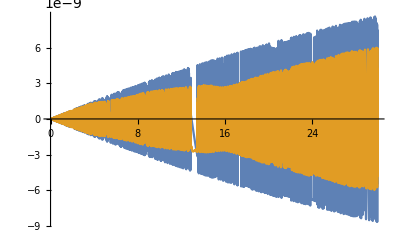

{1.73803,-0.045693,-1.63963,-0.0202168,-2.15736,-0.910775,2.72457,2.29077,3.90949,-5.25337,1.32876,1.97477,-0.404706,-1.06144,-0.477093,-5.08386,2.67514,1.9656,-1.77623,3.09595,4.8231,2.37364,1.46581,2.58395,4.63674,-1.94038,-3.98873,-0.168313,1.67939,-0.78348,0.598758,0.0521997,-0.864446,0.983704,2.06684,3.96568,-6.97717,0.848316,-1.33247,1.61222,1.77825,-0.624031,1.65492,-5.50362,6.41983,-1.80733,-0.266377,-5.66977,-1.06766,5.1265,4.90088,-6.3652,3.30168,1.73882,2.06253,-0.917298,3.63285,-1.46654,5.23585,0.0318235,0.673384,-1.1678,2.63649,-2.58931,-4.00008,1.09729,-0.658352,-1.0803,-4.22815,-2.98228,1.33887,2.1274,0.43313,2.78468,3.15288,1.99295,3.1618,-1.18631,0.305467,-1.23197,1.68291,-2.54248,-0.721309,4.45591,1.823,-2.16124,3.09862,2.78022,-1.37445,-0.800875,2.72714,5.60213,-2.68428,-2.84567,2.29851,1.36652,-2.71289,-4.81431,-2.2758,-3.0198,1.89251,-1.4574,-1.77936,1.05717,0.238008,-2.79007,-0.148574,2.09367,-2.10446,0.997186,1.92078,2.28959,3.27127,-2.31107,4.20395,3.49926,-3.33093,-1.32317,0.0769036,3.4817,7.52712,5.61886,-2.2662,3.82288,2.53089,1.13336,4.27856,-1.54211,-1.39142,-4.06257,-0.381513,-0.153588,2.93519,1.85658,-0.746164,0.722718,-5.95441,-0.894712,4.93573,0.544897,7.22713,0.0987081,-3.69665,1.1637,-1.31166,-0.133967,0.681505,5.17854,5.17087,1.77743,7.6931,-0.772111,-2.52656,2.58805,1.65755,-1.63957,-2.26591,0.848543,1.20715,-6.40465,4.92915,-1.40792,2.81424,-6.91561,-5.70777,1.82729,1.24333,-4.31596,-0.430978,3.10771,2.04917,-2.541,-0.731653,2.53969,-2.04034,-1.34036,0.000875684,-5.45727,-2.04564,0.363426,-0.925956,-1.52943,4.48167,-1.22175,6.50157,-3.66721,0.283874,2.5486,6.63032,7.2753,-2.95944,2.96994,-1.3016,-2.04421,0.738031,-2.6578,-6.23646,2.41723,1.39194,-0.653079,-4.82597,0.928545,2.6633,1.85336,1.08874,3.39663,0.553808,-6.03362,3.16556,-1.49566,5.45009,5.63318,0.659627,2.39132,-0.742525,-4.80235,-7.08296,-1.08107,1.72231,-0.826321,-5.8134,7.11542,-0.160149,-0.629165,-4.14621,-0.824996,6.03588,-0.793504,-0.0515581,-2.93141,-3.23505,3.39762,-1.63959,6.51016,4.85343,1.17124,1.12147,-1.74991,-4.05224,-0.105098,2.34929,-0.348131,2.19938,-0.0367957,-0.38719,-0.667442,-6.87678,1.74386,0.215017,2.62197,-0.553341,0.195631,0.260116,-2.88192,-4.06481,-4.09313,0.00941661,-0.148393,-0.390006,-5.6819,2.80977,-1.78015,-2.79338,0.582397,2.05655,-0.0490988,-1.46221,3.11339,-2.74654,1.72522,1.50666,0.949001,-1.31567,0.0109479,3.33641,3.53779,4.89806,-0.672907,-0.140849,3.24768,-3.47296,4.85782,-1.46543,0.497695,4.03052,0.808332,3.84987,2.32367,1.60211,-1.88753,-5.09262,2.0136,4.15945,-3.78105,-1.09578,0.0326788,-1.08238,3.28458,-1.73632,2.75053,-5.73605,3.36664,-0.539277,0.0086596,4.64393,0.0337825,-6.63018,1.67617,3.42541,-1.92704,4.33956,-0.440365,6.31895,-2.37612,-2.39353,3.91644,-1.20314,0.89625,-5.59755,3.40669,-7.22831,3.63338,-1.86634,-1.69643,0.258284,4.48331,3.42695,1.68663,-0.20899,-0.224465,3.99584,-5.50211,5.19774,-0.698053,-0.84678,-1.14994,-1.88302,-2.83782,1.17711,3.14722,0.748604,-1.2441,-3.42184,2.41386,3.65957,-1.85763,-1.27013,1.376,-1.10771,1.30301,2.7486,-0.967951,-6.65596,-0.312359,6.47458,3.80899,-0.279749,-4.18988,0.0691146,-2.90047,0.365897,0.751439,3.16904,-1.15799,-1.39098,4.48024,-2.64625,1.62052,3.54098,0.19948,-1.66745,-3.09105,1.66074,1.67913,1.51219,-0.586847,5.26766,1.34686,4.59014,-0.817039,1.12194,-0.931927,-2.07978,-4.57541,-1.97379,-1.31671,-0.0377309,2.00996,-1.94628,2.57069,3.5069,-0.657917,-1.86882,-3.88827,-2.41186,1.90609,3.45637,0.859677,0.00595033,2.51968,-0.883731,-2.93722,-1.4168,-2.39985,4.18482,-2.33281,-0.930329,2.53051,0.503328,-6.38722,4.81471,0.134615,1.57027,1.75281,2.38148,2.96035,-1.42324,-5.89782,0.722816,-2.25434,0.915425,-3.02527,0.306669,-2.24298,1.27063,2.31733,0.472455,1.59499,3.37562,0.451302,-5.40065,3.36172,5.49115,2.47501,-3.33182,1.0412,2.19844,7.06107,-1.46527,-1.81552,-1.92883,0.940205,-2.4619,3.97442,-5.72125,-0.212045,-7.4688,-0.585318,-0.487597,2.41236,1.35749,5.29907,-1.43342,3.67393,1.14997,-5.62702,-0.670578,1.71209,-1.22453,4.29449,0.618211,-3.02987,2.13991,-3.89193,1.02674,-3.54562,-6.71473,9.31726,4.62704,1.93131,-1.23466,0.384408,-2.80329,4.37768,3.23698,-0.414612,-1.38006,0.781635,5.65527,-4.26046,6.50721,2.43197,0.548758,-0.13004,-0.784865,2.28635,1.33722,1.29479,-3.79619,-0.3613,2.53681,3.01838,5.58401,1.8287,6.17522,-4.58111,-4.63578,2.44664,-0.52101,-3.31409,-4.41809,5.19969,4.88377,-0.716905,0.75577,-1.87672,-4.19752,-4.18911,-1.94223,0.942703,5.61486,-4.77546,1.30533,-0.504538,-3.84934,-0.559103,1.14596,0.00189254,1.93521,-1.10733,-0.166354,3.13523,-0.422794,-3.14382,-1.93048,1.2497,-2.35812,-0.141152,0.418076,4.38158,0.566024,-3.89322,-0.7248,-5.01708,-1.00641,-1.62104,-1.5379,-5.4414,0.359638,3.43125,-3.63461,-0.342704,-8.24397,5.1801,-1.55065,-0.93478,-1.12709,-0.720657,-1.51469,-1.10166,-6.22247,-0.0873413,2.78019,1.55086,-1.36377,-3.47973,-1.0353,-1.2714,0.995483,1.54923,1.7519,-1.0129,3.27368,-2.02568,5.22473,-2.43971,-1.52185,-3.17771,3.28123,0.916271,3.03007,-6.48083,-3.93478,-1.48914,-0.152588,-1.77075,4.09663,-1.80529,-3.57783,-2.10695,2.92741,3.30431,-4.26381,3.94952,-2.82159,-1.83569,1.62258,-2.94571,-1.4719,-2.10084,-3.29662,0.863266,-0.874021,-3.0072,0.5473,-1.32611,3.17039,0.276672,-2.51699,-3.99248,0.108733,5.60276,2.71714,1.60621,3.57038,-2.44165,0.528868,4.66578,1.94347,-1.07149,-7.97327,-3.16667,-0.874732,-1.26428,-0.454304,-2.78724,-0.0509204,-0.48744,3.16383,2.65746,2.00034,1.69803,-3.12447,-0.807749,-3.58735,3.09811,-1.07645,3.70466,2.96008,3.35224,-1.33687,-3.27291,0.861277,3.01725,-1.75255,-4.50217,5.52924,-4.52491,4.27063,3.58508,1.83003,-3.98807,1.8584,-5.44103,5.87936,3.9693,-2.23284,3.23194,-2.63377,-3.43192,8.35887,4.18068,0.231883,3.99803,1.08977,-1.25034,-2.98089,0.94357,1.23486,3.21135,2.54927,-2.88949,5.97738,-2.57108,1.3815,2.03497,1.98173,-8.23298,1.69326,-3.22029,-0.157425,-1.2807,-0.5237,-0.426843,1.10026,2.20347,-3.33271,2.44336,-2.5124,-1.6116,0.126302,-1.26877,1.29316,3.31321,2.34094,0.711823,2.21623,0.768147,-1.00498,-5.47234,-1.8616,0.991141,1.72035,1.12997,-1.48002,0.479064,1.06073,-3.73774,-2.87964,-1.14596,2.09403,3.95721,-3.38283,0.480901,3.20965,4.76363,0.507623,-4.96778,0.476681,-2.7146,-3.71245,3.15703,-2.40085,5.42971,-1.7363,2.6616,-0.742686,1.35213,0.743135,-1.24258,-0.980426,-1.91319,-1.7246,-1.54521,-2.05323,-1.60401,-1.75535,-3.26991,-2.90385,2.22168,-2.47096,3.10091,4.83409,1.06779,-0.275695,3.88795,-4.21923,4.4369,-1.11458,-2.04068,-3.03681,-1.8578,-3.5395,0.619308,0.37328,3.71366,-2.89792,0.69871,-1.22441,-2.66703,0.990002,2.17889,-0.186643,-0.750169,-3.84406,-3.0845,-1.88934,-5.42848,-2.53587,4.46966,2.26249,1.40025,1.83794,1.88816,5.38102,0.423031,3.08984,2.34212,3.69946,-0.844114,-2.75793,0.355815,-4.81996,1.40551,2.67682,2.30918,3.32277,2.03477,-0.277556,2.01171,2.95078,-4.3793,2.19829,2.50245,-1.95227,-1.05951,0.983545,0.898054,4.88906,1.11383,-0.916918,3.92746,2.96258,-1.29326,-4.76597,2.59842,5.68407,-2.78976,2.24652,-1.31912,3.74373,-8.99978,-0.702935,2.16238,-1.41581,0.892089,-4.98887,4.68721,1.80653,-0.00472178,0.896272,2.85109,-0.143278,-1.31864,-5.86846,2.45306,-1.29521,1.76761,-5.60924,-3.8759,-4.84155,-1.47183,-1.3372,4.93748,1.96866,3.58502,3.15987,0.681239,-1.16165,-2.52518,-3.52024,-2.51593,-0.975254,-0.913488,0.0540779,-2.98702,-3.18254,1.51874,4.44561,-2.64182,-2.54085,-2.81219,-2.73077,0.841061,7.24652,3.2119,-2.53592,-1.04532,0.673798,0.393805,2.74457,2.23559,0.447517,1.78894,-2.82656,-1.3165,-1.50358,-0.918002,-0.804759,-3.4337,-0.781073,-1.37295,3.27239,-6.89364,-3.84868,4.93046,1.66477,0.88998,-0.0152298,1.27609,2.0694,-7.26298,-2.18158,1.81298,1.66595,0.692796,-0.874039,-5.694,-2.9701,0.0916574,-2.39374,1.29145,2.72313,-2.29031,-1.11329,4.79098,0.702272,-1.20814,0.704098,-1.01254,-0.633787,-0.123576,3.3856,-8.16055,-1.46674,3.41902,1.79717,4.02773,-2.03919,-3.27114,-1.29319,-3.89151,0.503604,2.14641,4.46332,-2.93296,0.805181,-7.85231,-4.24155,1.7949,-2.31658,3.03588,-2.51669,3.91076,1.04503,-1.93795,3.67157,-5.56958,1.90808,0.555156,-2.8773,-3.92571,-4.9169,-1.44455,-1.34262,-3.84523,3.70279,-1.96838,0.763865,1.23625,-0.290616,-2.80048,-2.96725,3.83031,-0.165036,-1.51131,0.737429,-2.9539,2.8872,1.84126,-3.7209,4.87372,-3.02523,1.92884,1.18451,0.390055,-1.22464,-5.40909,4.60772,-0.622269,-2.83577,5.11001,3.82196,-1.90588,3.09869,-3.44509,-2.93949,-3.35845,2.45398,3.62272,-6.76285,0.98171,4.35431,-4.90559,1.92753,2.76829,1.53738,2.00349,-0.899551,1.31981,2.13521,-0.909366,-1.33461,1.08163,0.148229,-2.74002,-2.90961,2.54058,1.61721,3.45363,-1.3162,-0.0806315,4.58079,0.347464,1.8232,-2.62775,1.02557,-1.67148,4.27673,2.84046,2.70309,-0.264137,-2.41537,-1.16267,2.46508,-2.75651,-2.37606,-0.49287,3.80622,0.0186605}

```mathematica
(*Generate a Complete Set of Functions Modeling the System's Behavior, Using the BC Lists Above*)
func[t_]:=Piecewise[Table[{x[t-(i-1)*tjit,xBCList[[i]],vBCList[[i]],(i-1)*tjit,delOmegaList[[i]]],(i-1)*tjit<t<i*tjit},{i,1,num}]]
Plot[{Re[x[t,0,0,0,0]],Re[func[t]]},{t,0,num*tjit}, PlotRange -> All]
(*Plot[{Re[func[t]]},{t,0,num*tjit}]*)
Print[delOmegaList]
```

```mathematica
(*Compute Power Suppression Factor*)
SystemPowerWMicrophonics=NIntegrate[Re[func[t]]^2,{t,0.9*num*tjit,num*tjit}]
SystemPowerWOMicrophonics=NIntegrate[Re[x[t,0,0,0,0]]^2,{t,0.9*num*tjit,num*tjit}]
PowerSuppression=SystemPowerWMicrophonics/SystemPowerWOMicrophonics
AbsSystemPowerWMicrophonics=NIntegrate[Abs[func[t]]^2,{t,0.9*num*tjit,num*tjit}]
AbsSystemPowerWOMicrophonics=NIntegrate[Abs[x[t,0,0,0,0]]^2,{t,0.9*num*tjit,num*tjit}]
AbsPowerSuppression=AbsSystemPowerWMicrophonics/AbsSystemPowerWOMicrophonics
```

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 5.0263×10^-17 and 2.21733×10^-18 for the integral and error estimates.

5.0263×10^-17

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {29.98545223740929297796820041099863374256528913974761962890625}. NIntegrate obtained 1.04829×10^-16 and 2.9607×10^-18 for the integral and error estimates.

1.04829×10^-16

0.479475

1.008×10^-16

2.09457×10^-16

0.481246